# Лабароторная работа 2 Дунаев Виктор 3 курс, 6 группа

## Задание 1

```mathematica
(* условие и графие *)
```

```mathematica
f[t_,α_]:=Exp[-((t^2)/2)]*Exp[i*α*t]
```

```mathematica
f[t,α]
```

ⅇ^(-t^2/2+i t α)

```mathematica
Manipulate[Plot[f[t,α], {t, -5, 5}], {α, 0, 1}]
```

```mathematica
(* прямое преобразование *)
```

```mathematica
FourierTransform[f[t,1],t,w]
```

ⅇ^(1/2 (i+ⅈ w)^2)

```mathematica
(* обратное преобразование *)
```

```mathematica
r= InverseFourierTransform[%, w, t]
```

ⅇ^(i t-t^2/2)

```mathematica
Plot[r,{t,-5,5}]
```

-Graphics-

## Задание 2

```mathematica
(* условие *)
```

```mathematica
f[t_]:=(
answer = 0;
If[0<=t≤5,answer=cos((t^2)/3),answer=0];
answer
)
```

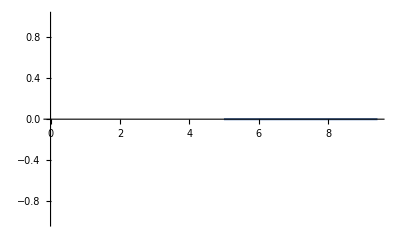

```mathematica
Plot[f[t],{t,0,3Pi}]
```

```mathematica
(* косинус - преобразование фурье *)
```

```mathematica
q = FourierCosTransform[cos((t^2)/3),t,ω]
```

-1/3 cos √(2 π) DiracDelta''[ω]

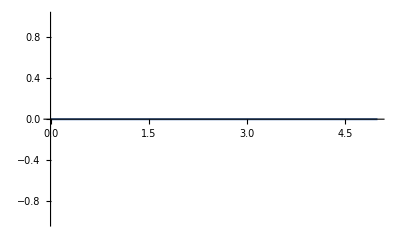

```mathematica
Plot[q,{ω,0,5}]
```

## Задание 3

```mathematica
(* синус - преобразование фурье *)
```

```mathematica
f[t_]:=(
answer = 0;
If[0<=t≤10,answer=sin((t^2)/3),answer=0];
answer
)
```

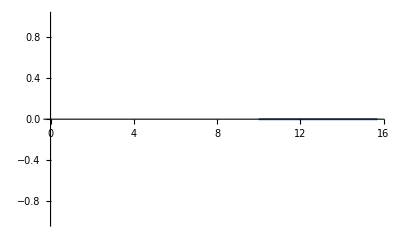

```mathematica
Plot[f[t],{t,0,5Pi}]
```

```mathematica
q = FourierSinTransform[sin((t^2)/3),t,w]
```

-(2 √(2/π) sin)/(3 w^3)

```mathematica
Plot[q,{w,0,5}]
```

-Graphics-

## Задание 4

```mathematica
(* условие *)
```

```mathematica
f[t_]:=Piecewise[{{1-Abs[t], Abs[t]<1}, {0, Abs[t]≥1}}]
```

```mathematica
v[t_]:=Piecewise[{{1, Abs[t]<2}, {0, Abs[t]≥2}}]
```

```mathematica
Convolve[f[t],v[t],t,y]
```

Piecewise[{{1, -1<y≤1}, {1/2 (1-2 y-y^2), -2<y≤-1}, {1/2+y-y^2/2, 1<y<2}, {1/2 (-3+y)^2, 2≤y<3}, {1/2 (3+y)^2, -3<y≤-2}, {0, True}}]

```mathematica
(* свертка *)
```

```mathematica
consolve[N]:=(
f[t_]:=Piecewise[{{1-Abs[t], Abs[t]<1}, {0, Abs[t]≥1}}];
v[t_]:=Piecewise[{{1, Abs[t]<2}, {0, Abs[t]≥2}}];
F=0;
For[i=0,i<=N,i++,
F+=Integrate[f[t]*v[i-t],{t,0,i}];
];
F
)
```

```mathematica
consolve[2]
```

consolve[2]